```mathematica
;;;
```

Last updated:   Wed 12 Jul 2023
Author:   Martins Dogo

# QUB Lanyon Building in 3d

```mathematica
i=-Graphics-;
```

```mathematica
i2=ImageTake[i,{300,-1},{100,-100}];
```

```mathematica
i3=DeleteBorderComponents[Binarize@i2];
i4=ImageGraphics[i3];
```

```mathematica
ℛ1=DiscretizeGraphics[i4]
```

```mathematica
ℛ2=BoundaryDiscretizeGraphics[i4];
```

```mathematica
(*  ℛ1 *)
```

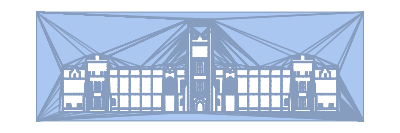

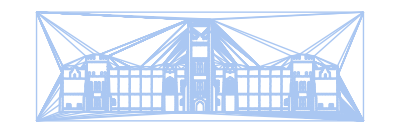

```mathematica
(* ℛ2 *)
```

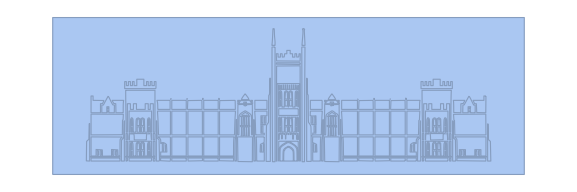

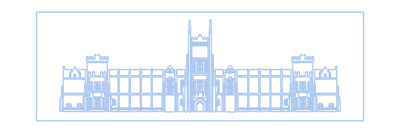

```mathematica
(* --- --- --- *)
```

```mathematica
RegionProduct[ℛ2,Line[{{0.},{50.}}]]
```

-Graphics3D-